# Fully implicit scheme for thin layer voltammetry

Version 1.30
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.7]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
optionA={
PlotStyle-> {Red,AbsoluteThickness[0.7]},
FrameLabel-> {
Style["increment",FontFamily-> "Arial" ,FontSize->  12,FontColor->Black],
Style["χ",FontFamily->  "Times New Roman" ,FontSize->   12, FontWeight->   "Plain",FontColor-> Black],
None,
None}
};
```

```mathematica
optionB={
PlotStyle->{Red,AbsoluteThickness[0.7]},
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12,FontColor->Black, FontSlant->Italic],
Style["χ",FontFamily-> "Times New Roman",FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None}
};
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeDiagonals];

makeDiagonals[m_Integer,d_]:=
	Module[{x,y,z},
		x=Table[-d,{m-3}];
		z=Table[-d,{m-3}];
		y=Table[1.+2.*d,{m-2}];
{x,y,z}]
```

```mathematica
{x,y,z}=makeDiagonals[7,𝔻]
```

{{-𝔻,-𝔻,-𝔻,-𝔻},{1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻},{-𝔻,-𝔻,-𝔻,-𝔻}}

```mathematica
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},5]
```

SparseArray[<13>,{5,5}]

```mathematica
Normal@mat[[1]]
```

{1.+2. 𝔻,-𝔻,0,0,0}

```mathematica
MatrixForm@mat
```

(1.+2. 𝔻 | -𝔻 | 0 | 0 | 0
-𝔻 | 1.+2. 𝔻 | -𝔻 | 0 | 0
0 | -𝔻 | 1.+2. 𝔻 | -𝔻 | 0
0 | 0 | -𝔻 | 1.+2. 𝔻 | -𝔻
0 | 0 | 0 | -𝔻 | 1.+2. 𝔻)

```mathematica
mat⟦1,1⟧="Y1"
mat⟦1,2⟧="Z1"
```

Y1

Z1

```mathematica
mat⟦-1,-1⟧="Y_1"
mat⟦-1,-2⟧="X"
```

Y_1

X

## Set Up Solution

```mathematica
Clear[implicitSolveTLV];

implicitSolveTLV[m_Integer,n_Integer,d_,{lowerLimit_,upperLimit_},{ksStar_,α_}]:=Module[{x,y,z,len,mat,x1,y1,z1,initial,range,τ,solveNext},

range=2*(upperLimit+Abs[lowerLimit]);
τ=range/(n-1.);

{x,y,z}=makeDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
x1=x⟦1⟧;
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[1.,{m}];

solveNext[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2},

ξ=If[k>(n+1)/2,Exp[upperLimit-range+(τ*k)],Exp[upperLimit-(τ*k)]];

tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));

b=list[[2;;-2]];
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b⟦-1⟧+=(tmp*d*ksStar*ξ^(1.-α));
mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;
mat⟦-1,-1⟧=y1-4.*d*tmp;
mat⟦-1,-2⟧=x1+d*tmp;

tmp2=LinearSolve[mat,b];
Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,(ksStar*ξ^(1.-α)+4.*tmp2⟦-1⟧-tmp2⟦-2⟧)*tmp}]
];

FoldList[solveNext,initial,Range[2,n]]
]
```

## Set Parameter Values

### Variables/ constants

```mathematica
Clear[F,R,T,f,𝒟,α];

F=96485.(*Faradays constant*);

R=8.3144(*gas constant*);

T=298.(*temperature*);

f=F/(R*T);

𝒟=1.*^-5(*diffusion coefficient*);
```

### Electrochemical variables

```mathematica
Clear[α,upperLimit,lowerLimit,𝕥];

α=0.5 (*transfer coefficient*);

lowerLimit=-10.(*limit = f×(E-E^o)*);

upperLimit=10.(*limit = f×(E-E^o)*);

𝕥=2.*(upperLimit+Abs[lowerLimit]);
```

### Simulation variables

To achieve the "ideal" response with a dimensionless peak height of 0.25 for the reversible voltammogram you need large values of n and 𝔻 to ensure that m>20.

```mathematica
Clear[n,𝔻,τ,𝕃,Δx,ksDim,ksStar,m];

n=Round[𝕥/(.001*f)];(*1mV steps*);


τ=𝕥/(n-1);(*calculation of the incremental time/potential step*)

𝕃=1.*^1;(*= (L^2 σ)/𝒟 *)

Δx=.01;

𝔻=𝕥/(𝕃*Δx*Δx*(n-1));

m=1+Ceiling[1/Δx];

ksDim=2.*^1;(*dimensionless rate constant*)

ksStar=2.*ksDim*𝕃*Δx;
```

```mathematica
{n,𝔻,τ,𝕃,Δx,ksDim,ksStar,m}
```

{1027,38.9864,0.0389864,10.,0.01,20.,4.,101}

## Solve

```mathematica
c=implicitSolveTLV[m,n,𝔻,{lowerLimit,upperLimit},{ksStar,α}];
```

## Plot CV

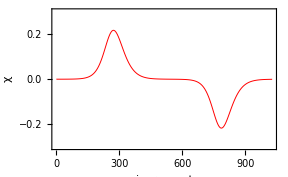

```mathematica
cv1=Map[((-#⟦3⟧+(#⟦2⟧*4)-#⟦1⟧*3)*1/(𝕃*Δx))&,c];

plot1=ListPlot[cv1,optionA,PlotRange->{{0,n},{-0.3,.3}}]
```

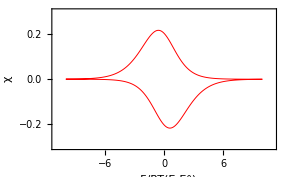

```mathematica
cv2=Table[{If[j>(n+1)/2,upperLimit-𝕥+((j-1)*τ),upperLimit-((j-1)*τ)],cv1⟦j⟧},{j,1,Length[cv1]}];

plot2=ListPlot[cv2,optionB,PlotRange->{{upperLimit+1,lowerLimit-1},{-0.3,.3}}]
```

```mathematica
peakHeight=Min[cv2⟦All,2⟧];
Select[cv2,#⟦2⟧==peakHeight&]//Flatten;
Print["peak at ",%⟦1⟧*1000/f," mV with height ",peakHeight]
```

peak at 15.5179 mV with height -0.2168

Alternatively plot the CV on the semi-infinite diffusion scale:

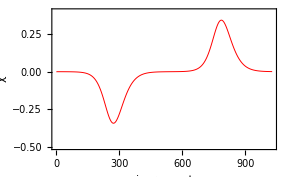

```mathematica
cv1=Map[((#⟦3⟧-(#⟦2⟧*4)+#⟦1⟧*3)*√((𝔻*(n-1))/(4.*𝕥)))&,c];

plot1=ListPlot[cv1,optionA,PlotRange->{{0,n},{-0.5,.4}}]
```

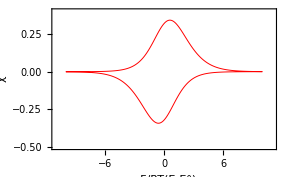

```mathematica
cv2=Table[{If[j>(n+1)/2,upperLimit-𝕥+((j-1)*τ),upperLimit-((j-1)*τ)],cv1⟦j⟧},{j,1,Length[cv1]}];

plot2=ListPlot[cv2,optionB,PlotRange->{{upperLimit+1,lowerLimit-1},{-0.5,0.4}}]
```